## Stabilization in finite time (Sun et al., PRL 2017)

```mathematica
Clear["Global`*"];
```

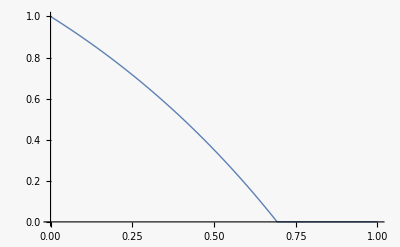

```mathematica
tmax=1;
sol=NDSolveValue[{x'[t]==x[t]-k Sign[x[t]]/.{k->2},x[0]==1},x,{t,0,tmax}];
Plot[sol[t],{t,0,tmax},PlotRange->All]
```

```mathematica
sol1=DSolveValue[{x'[t]==x[t]-k ,x[0]==x0},x[t],t,Assumptions->0<x0<1]//Simplify
```

k-ⅇ^t k+ⅇ^t x0

```mathematica
Solve[{sol1==0,k>1>x0>0,t>0},t]
```

{{t→ConditionalExpression[Log[k/(k-x0)], k>1&&0<x0<1]}}

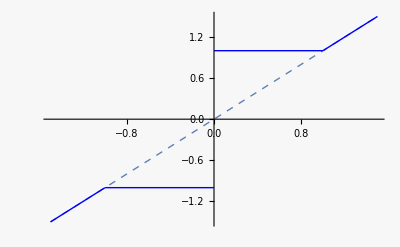

```mathematica
u[x_,k_]:=k Piecewise[{{x, Abs[x]≥1},{Sign[x],Abs[x]<1}}]
Plot[{x,u[x,1]},{x,-1.5,1.5},PlotStyle->{{Thin,Dashed},{Thick,Blue}}]
```

```mathematica
Manipulate[Plot[{k^2 Log[k/(k-x0)],(k^2 x0^2)/(2(k-1))},{k,1,3},PlotRange->{0,2},PlotLabels->{"E_NL","E_L"}],{{x0,0.5},0.01,0.99}]
```